## Coupled Entropy NSP & Paper 2025

```mathematica
$Assumptions = κ>0&&κ∈Reals&&x∈Reals&& μ∈Reals&&σ∈Reals&&σ>0&&α∈Reals&&α>0&&d∈Integers&&d>0&&γ∈ Reals && 0<γ<∞
```

κ>0&&κ∈ℝ&&x∈ℝ&&μ∈ℝ&&σ∈ℝ&&σ>0&&α∈ℝ&&α>0&&d∈ℤ&&d>0&&γ∈ℝ&&0<γ<∞

### Compute Entropies of Gen. Pareto Distribution

```mathematica
Clear[CECoupledExp]
```

```mathematica
Assuming[κ>0&&x>0,
CoupledExponentialDistribution[κ,0,σ]
]
```

ProbabilityDistribution[Piecewise[{{If[κ≠0,If[Simplify[1-(κ (-x))/σ]>0,(1-(κ (-x))/σ)^(-(1+1 κ)/(1 κ)),0],Exp[-x/σ]]/σ, x≥0}, {0, True}}],{x,-∞,∞}]

κ>0&&κ∈ℝ&&x∈ℝ&&μ∈ℝ&&σ∈ℝ&&σ>0&&α∈ℝ&&α>0&&d∈ℤ&&d>0

This computes the Coupled Entropy of the Pareto Distribution.  See below for computation of the coupled probability 
and the coupled logarithm of the distribution

```mathematica
-∫_0^∞ ((1+κ) σ^(1+1/κ) (x κ+σ)^(-2-1/κ))((1-(σ^(1/κ) (x κ+σ)^(-(1+κ)/κ))^(-1+1/(1+κ)))/κ)ⅆx//FullSimplify
```

(-1+(1+κ) σ^(κ/(1+κ)))/κ

```mathematica
(1+κ)CoupledLogarithm[σ^-1,κ,1,1]-(1+κ)/κ//FullSimplify
```

-((1+κ) σ^(κ/(1+κ)))/κ

```mathematica
SECoupledExp[κ_,σ_]:=1+κ Log[σ];
```

```mathematica
CECoupledExp[κ_,σ_]:=(-1+(1+κ) σ^(κ/(1+κ)))/κ;
```

(-1+(1+κ) σ^(κ/(1+κ)))/κ = (1+κ)/κ(σ^(κ/(1+κ))-1)+(1+κ)/κ-1/κ=1+ln_((1+κ)/κ)σ  Confirms 2025 Solution

```mathematica
TECoupledExp[κ_,σ_] := (1+κ-σ^(-1+1/(1+κ)))/κ
```

```mathematica
(1+κ-σ^(-1+1/(1+κ)))/κ//FullSimplify
```

(1+κ-σ^(-1+1/(1+κ)))/κ

(1+κ-σ^(-1+1/(1+κ)))/κ= 1 - 1/κ(σ^(-κ/(1+κ))-1) Confirms 2025 Result

```mathematica
NTECoupledExp[κ_,σ_]:=((1+κ) (-1+(1+κ) σ^(κ/(1+κ))))/κ
```

```mathematica
CoupledProbability[
ProbabilityDistribution[1/σ(1-(κ (-x))/σ)^(-(1+1 κ)/(1 κ)),{x,0,∞}],
(- κ)/(1+κ),x
]
```

Piecewise[{{0, x≤0}, {(1+κ) σ^(1+1/κ) (x κ+σ)^(-2-1/κ), True}}]

```mathematica
CoupledLogarithm[
1/σ(1-(κ (-x))/σ)^(-(1+1 κ)/(1 κ)),
κ,1,1]//FullSimplify
```

ConditionalExpression[(1-(σ^(1/κ) (x κ+σ)^(-(1+κ)/κ))^(-1+1/(1+κ)))/κ,(x κ+σ)^(-1-1/κ)≥0]

```mathematica
Assuming[κ>0,CoupledEntropy[
Assuming[κ>0&&x>0,
CoupledExponentialDistribution[κ,0,σ]
],κ,1,1]]//Simplify
```

-∫_0^∞ If[(Piecewise[{{σ^(1/κ) (x κ+σ)^(-1-1/κ), x≥0}, {0, True}}])≥0,If[κ≠0,-1/(1 κ)((Piecewise[{{If[κ≠0,If[Simplify[1-(κ (-x))/σ]>0,(1-(κ (-x))/σ)^(-(1+1 κ)/(1 κ)),0],Exp[-x/σ]]/σ, x≥0}, {0, True}}])^(-κ/(1+1 κ))-1),Log[Piecewise[{{If[κ≠0,If[Simplify[1-(κ (-x))/σ]>0,(1-(κ (-x))/σ)^(-(1+1 κ)/(1 κ)),0],Exp[-x/σ]]/σ, x≥0}, {0, True}}]]],Undefined] (Piecewise[{{0, x<0}, {(1+κ) σ^(1+1/κ) (x κ+σ)^(-2-1/κ), True}}])ⅆx

```mathematica
NSECoupledExp[κ_,σ_]:=
Assuming[∞>κ>0,
Piecewise[{
{NShannonEntropy[CoupledExponentialDistribution[κ,0,σ],0,100],0<κ<0.09},
{NShannonEntropy[CoupledExponentialDistribution[κ,0,σ],0,1000],0.09≤κ<0.74},
{NShannonEntropy[CoupledExponentialDistribution[κ,0,σ],0,10000],0.74≤κ<1.5},
{NShannonEntropy[CoupledExponentialDistribution[κ,0,σ],0,15000],1.5≤κ}
}]
]
```

```mathematica
NSECoupledExp[#,1]&/@{0.25,0.5,0.75,1,1.25}
```

{1.25,1.49992,1.74985,1.99796,2.23985}

```mathematica
NSECoupledExp[0.01,0.25]
```

-0.376294

```mathematica
NSECoupledExp[2,2]
```

3.54523

### Plot Comparison of GPD with TE, NTE, & Shannon

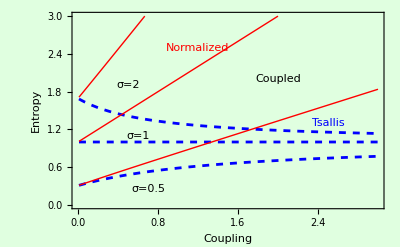

```mathematica
Assuming[0<κ<∞,
Plot[
{
(*Table[SECoupledExp[κ,σ],{σ,{0.5,1,2}}],*)
{Style[Table[TECoupledExp[κ,σ],{σ,{0.5,1,2}}],
{Blue,Dashed}]},
{Style[Table[NTECoupledExp[κ,σ],{σ,{0.5,1,2}}],
{Red,Dotted}]},
{Style[Table[CECoupledExp[κ,σ],{σ,{0.5,1,2}}],
Black]}
},
{κ,0.01,3},
Background->LightGreen,
PlotRange->{{0,3},{0,3}} ,
Frame->{{True,False},{True,False}},
FrameLabel->{"Coupling","Entropy"},
FrameStyle->Directive[10,Bold,Black],
Epilog->{
Inset[Style["Coupled",Black,Medium],{2,2}],
Inset[Style["Tsallis",Blue,Medium],{2.5,1.3}],
Inset[Style["Normalized",Red,Medium],{1.2,2.5}],
Inset[Style["σ=2",Black],{0.5,1.9}],
Inset[Style["σ=1",Black],{0.6,1.1}],
Inset[Style["σ=0.5",Black],{0.7,0.25}]
}
]
]
```

#### Compute Tsallis Entropy with different q values

```mathematica
$Assumptions=κ∈Reals&&0<κ<∞&&α∈Reals&&0<α<∞&&d∈Reals&&0<d<∞&&σ∈Reals&&0<σ<∞
```

κ∈ℝ&&0<κ<∞&&α∈ℝ&&0<α<∞&&d∈ℝ&&0<d<∞&&σ∈ℝ&&0<σ<∞

qEnt = 1/qDist

```mathematica
∫_0^∞ FullSimplify[1/σ(1+(κ x)/σ)^(-(1+ κ)/κ)(1+qToCoupling[(1+κ)/(1+2κ)])CoupledLogarithm[σ(1+(κ x)/σ)^((1+κ)/κ),qToCoupling[(1+κ)/(1+2κ)],1]]ⅆx//FullSimplify
```

```mathematica
∫_0^∞ 1/((2+5 κ) (x κ+σ))2 (1+2 κ) (1+(x κ)/σ)^(-1/κ) If[(1+(x κ)/σ)^(1/κ) (x κ+σ)≥0,If[-(1-(1+κ)/(1+2 κ))/(3-(1+κ)/(1+2 κ))≠0,-(((1+(x κ)/σ)^((1+κ)/κ) σ)^(-(1-(1+κ)/(1+2 κ))/((3-(1+κ)/(1+2 κ)) (1+-(1-(1+κ)/(1+2 κ))/(3-(1+κ)/(1+2 κ)))))-1)/((1-(1+κ)/(1+2 κ))/(3-(1+κ)/(1+2 κ))),Log[(1+(x κ)/σ)^((1+κ)/κ) σ]],Undefined]ⅆx
```

```mathematica
2/((2+5 κ) (x κ+σ))(1+2 κ) (1+(x κ)/σ)^(-1/κ) (-(((1+(x κ)/σ)^((1+κ)/κ) σ)^(-(1-(1+κ)/(1+2 κ))/((3-(1+κ)/(1+2 κ)) (1+-(1-(1+κ)/(1+2 κ))/(3-(1+κ)/(1+2 κ)))))-1)/((1-(1+κ)/(1+2 κ))/(3-(1+κ)/(1+2 κ))))//FullSimplify
```

-(2 (1+2 κ) (1+(x κ)/σ)^(-1/κ) (-1+((1+(x κ)/σ)^(1/κ) (x κ+σ))^(-κ/(2+4 κ))))/(κ (x κ+σ))

```mathematica
∫_0^∞ -(2 (1+2 κ) (1+(x κ)/σ)^(-1/κ) (-1+((1+(x κ)/σ)^(1/κ) (x κ+σ))^(-κ/(2+4 κ))))/(κ (x κ+σ))ⅆx//FullSimplify
```

-(2 (1+2 κ) σ^(1/κ) (-σ^(-1/κ)+((2+4 κ) σ^(-(2+4 κ+κ^2)/(2 κ+4 κ^2)))/(2+κ (5+κ))))/κ

qEnt = 2-qDist

```mathematica
∫_0^∞ FullSimplify[1/σ(1+(κ x)/σ)^(-(1+ κ)/κ)(1+qToCoupling[1-κ/(1+κ)])CoupledLogarithm[σ(1+(κ x)/σ)^((1+κ)/κ),qToCoupling[1-κ/(1+κ)],1]]ⅆx//FullSimplify
```

(2 (1+κ) (1-(2 σ^(-κ/(2+2 κ)))/(2+κ)))/κ

Dual kEnt = - κ/(1+κ)

```mathematica
∫_0^∞ FullSimplify[1/σ(1+(κ x)/σ)^(-(1+ κ)/κ)(1-κ/(1+κ))CoupledLogarithm[σ(1+(κ x)/σ)^((1+κ)/κ),-κ/(1+κ),1]]ⅆx//FullSimplify
```

(1-σ^-κ/(1+κ+κ^2))/κ

### Coupled Entropy of Coupled Stretched Exponential Distribution

Structure of solution is d/α+Log_((α κ)/(1+d κ))[Z_κ(σ,α,d)]=d/α+Log_((α κ)/(1+d κ))[σ]⊕_((α κ)/(1+d κ))Log_((α κ)/(1+d κ))[Z'_κ(α,d)]

Computation of Coupled Entropy of Coupled Stretched Exponential

```mathematica
Clear[CoupledEntropyCSE];
CoupledEntropyCSE[σ_,κ_,α_,d_]:=
CoupledEntropyCSE[σ,κ,α,d]=
d/α+CoupledLogarithm[
NormMultiCoupled[σ,κ,α,d],
(α κ)/(1+d κ), 0];
```

Plot of Coupled Entropies

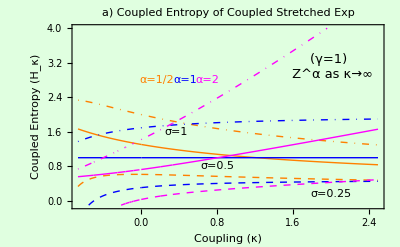

```mathematica
Plot[
Evaluate@{
Table[CoupledEntropyCSE[σ,κ,1/2,1]^1,{σ,{0.25,0.5,1}}],
Table[CoupledEntropyCSE[σ,κ,1,1]^1,{σ,{0.25,0.5,1}}],
Table[CoupledEntropyCSE[σ,κ,2,1]^1,{σ,{0.25,0.5,1}}],
},
{κ,-0.667,2.5},
Background->LightGreen,
PlotRange->{{-0.667,2.5},{-0.1,4}} ,
Frame->{{True,False},{True,False}},
FrameLabel->{"Coupling (κ)","Coupled Entropy (H_κ)"},
FrameStyle->Directive[10,Bold,Black],
PlotStyle->Flatten[Table[{αCol,σCol},{αCol,{{Orange,Thickness[Medium]},{Blue,Thickness[Large]},{Magenta,Thickness[Medium]}}},{σCol,{Dashed,,DotDashed}}],1],
PlotLabel->
"a) Coupled Entropy of Coupled Stretched Exp",
Epilog->{
Inset[Style["α=1/2",Orange,Medium],{.16,2.8}],Inset[Style["α=1",Blue,Medium],{.46,2.8}],
Inset[Style["α=2",Magenta,Medium],{.7,2.8}],
Inset[Style["σ=1",Black],{0.37,1.6}],
Inset[Style["σ=0.5",Black],{0.8,.8}],
Inset[Style["σ=0.25",Black],{2.0,0.17}],
Inset[Style[DisplayForm[HoldForm[(γ=1)"
 Z^α as κ→∞"]],Black,FontSize->13],{2,3.1}]
}
]
```

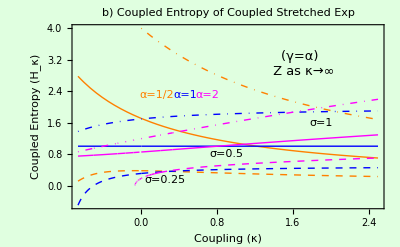

```mathematica
Plot[
Evaluate@{
Table[CoupledEntropyCSE[σ,κ,1/2,1]^(2/1),{σ,{0.25,0.5,1}}],
Table[CoupledEntropyCSE[σ,κ,1,1],{σ,{0.25,0.5,1}}],
Table[CoupledEntropyCSE[σ,κ,2,1]^(1/2),{σ,{0.25,0.5,1}}],
},
{κ,-0.667,2.5},
Background->LightGreen,
PlotRange->{{-0.667,2.5},{-.5,4}} ,
Frame->{{True,False},{True,False}},
FrameLabel->{"Coupling (κ)","Coupled Entropy (H_κ)"},
FrameStyle->Directive[10,Bold,Black],
PlotStyle->Flatten[Table[{αCol,σCol},{αCol,{{Orange,Thickness[Medium]},{Blue,Thickness[Large]},{Magenta,Thickness[Medium]}}},{σCol,{Dashed,,DotDashed}}],1],
PlotLabel->
"b) Coupled Entropy of Coupled Stretched Exp",
Epilog->{
Inset[Style["α=1/2",Orange,Medium],{.16,2.3}],Inset[Style["α=1",Blue,Medium],{.46,2.3}],
Inset[Style["α=2",Magenta,Medium],{.7,2.3}],
Inset[Style["σ=1",Black],{1.9,1.6}],
Inset[Style["σ=0.5",Black],{0.9,.8}],
Inset[Style["σ=0.25",Black],{0.25,0.15}],
Inset[Style[DisplayForm[HoldForm[(γ=α)"
 Z as κ→∞"]],Black,FontSize->13],{1.7,3.1}]
}
]
```

Plot with variable dimensions

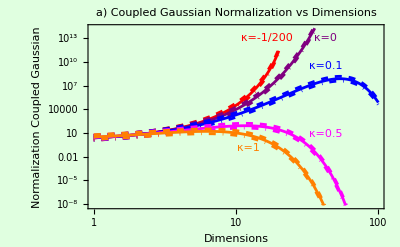

```mathematica
LogLogPlot[
Evaluate@{
Table[NormMultiCoupled[σ,-0.5 10^-1,2,d],{σ,{0.5,1,2}}],Table[NormMultiCoupled[σ,0.0,2,d],{σ,{0.5,1,2}}],
Table[NormMultiCoupled[σ,0.1,2,d],{σ,{0.5,1,2}}],
Table[NormMultiCoupled[σ,0.5,2,d],{σ,{0.5,1,2}}],
Table[NormMultiCoupled[σ,1.0,2,d],{σ,{0.5,1,2}}],
},
{d,1,100},
Background->LightGreen,
PlotRange->{{0,100},{0,Automatic}} ,
Frame->{{True,False},{True,False}},
FrameLabel->{"Dimensions","Normalization Coupled Gaussian"},
FrameStyle->Directive[10,Bold,Black] ,
PlotStyle->Flatten[Table[{κCol,σCol},{κCol,{Red,Purple,Blue,Magenta,Orange}},{σCol,{DotDashed,,Dashed}}],1],
PlotLabel->"a) Coupled Gaussian Normalization vs Dimensions",
Epilog->{
Inset[Style["κ=-1/200",Red,Medium],{2.8,30}],Inset[Style["κ=0",Purple,Medium],{3.75,30}],
Inset[Style["κ=0.1",Blue,Medium],{3.75,22}],
Inset[Style["κ=0.5",Magenta,Medium],{3.75,2}],
Inset[Style["κ=1",Orange,Medium],{2.5,-2}],
(*Inset[Style["σ=2",Black],{1.45,1.45}],
Inset[Style["σ=1",Black],{0.8,.8}],
Inset[Style["σ=0.5",Black],{0.5,0.1}]*)
}
]
```

With γ = 2/10

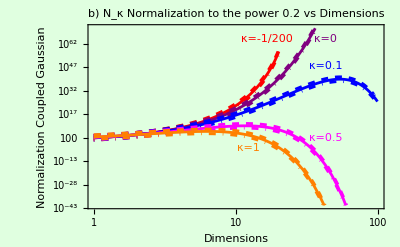

### Score Function Plots

The score function of the GPD is -σ^-1, which is a powerful description of the scales unique properties.
The score function is computed from the derivative of the log of the pdf.

```mathematica
NegDerGPD[σ_,κ_,x_]:=(1+κ)/(x κ+σ);
NegDerGPDq[β_,q_,x_]:=β/(1+(-1+q) x β);
```

```mathematica
Clear[NegDerGPD]
```

```mathematica
Assuming[0<κ<∞,-D[Log[1/σ(1+(κ x)/σ)^(-(1+κ)/κ)],x]]//FullSimplify
```

(1+κ)/(x κ+σ)

```mathematica
(1+κ)/(x κ+σ)/.{κ->(-(1-q))/(2-q),σ->1/((2-q)β)}//FullSimplify
```

β/(1+(-1+q) x β)

Plot -β Score versus x/β

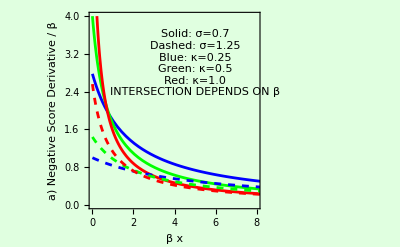

```mathematica
Plot[MapThread[scaleShapeToBeta[#1,#2,1]
NegDerGPD[#1,#2,scaleShapeToBeta[#1,#2,1]x]&,{{0.75,0.75,0.75,1.25,1.25,1.25},{0.25,0.5,1,0.25,0.5,1}}]//Evaluate,{x,0.0001,10},
Background->LightGreen,
PlotRange->{{0,8},{0,4}},
PlotStyle->{Blue,Green, Red,{Blue,Dashed},{Green,Dashed},{Red,Dashed}},
Epilog->Inset[Style[Text["Solid: σ=0.7
Dashed: σ=1.25
Blue: κ=0.25
Green: κ=0.5
Red: κ=1.0
INTERSECTION DEPENDS ON β"],Larger],{5,3}],
LabelStyle->Directive[Bold, Medium],
Frame->{{True,True},{True,True}},
FrameLabel->{{"a) Negative Score Derivative / β",""},{"β x",
"a) Negative Score Derivative for q-Exponential"}}
]
```

Translation of sigma and kappa

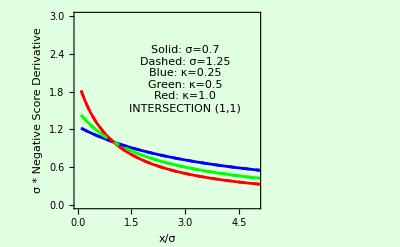

```mathematica
Plot[MapThread[
#1 NegDerGPD[#1,#2, #1x]&,{{0.75,0.75,0.75,1.25,1.25,1.25},{0.25,0.5,1,0.25,0.5,1}}]//Evaluate,{x,0.1,10},
Background->LightGreen,
PlotRange->{{0,5},{0,3}},
PlotStyle->{Blue,Green, Red,{Blue,Dashed},{Green,Dashed},{Red,Dashed}},
Epilog->Inset[Style[Text["Solid: σ=0.7
Dashed: σ=1.25
Blue: κ=0.25
Green: κ=0.5
Red: κ=1.0
INTERSECTION (1,1)"],Larger],{3,2}],
LabelStyle->Directive[Bold, Medium],
Frame->{{True,True},{True,True}},
FrameLabel->{{"σ * Negative Score Derivative",""},
{"x/σ","a) Negative Score Derivative for Coupled Exponential"}}
]
```

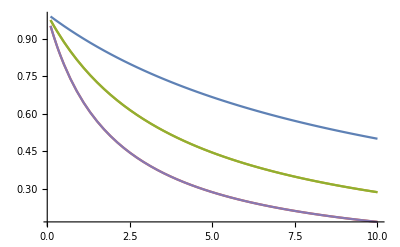

```mathematica
Plot[MapThread[#1^-1 NegDerGPDq[#1,#2,#1^-1 x]&,{{0.5,0.5,.2,.2,.5},{1.1,1.25,1.25,1.5,1.5}}]//Evaluate,{x,0.1,10}]
```

### Generalized Weibull Distribution

```mathematica
GWDSF[σ_,κ_,α_,x_]:=(1+(κ x^α)/σ^α)^(-1/(α κ));
```

```mathematica
GWDPDF[σ_,κ_,α_,x_]:=x^(α-1)/σ^α(1+(κ x^α)/σ^α)^(-1/(α κ)-1);
```

```mathematica
D[-Log[GWDPDF[σ,κ,α,x]],x]\\FullSimplify
```

Syntax::tsntxi: "D[-Log[GWDPDF[σ,κ,α,x]],x]\\FullSimplify" is incomplete; more input is needed.

```mathematica
D[-Log[x^(α-1)/σ^α(1+(κ x^α)/σ^α)^(-1/(α κ)-1)],x]\\FullSimplify
```

Syntax::tsntxi: "D[-Log[x^(α-1)/σ^α(1+(κ x^α)/σ^α)^(-1/ακ-1)],x]\\FullSimplify" is incomplete; more input is needed.

```mathematica
-D[Log[x^(-1+α) σ^-α (1+x^α κ σ^-α)^(-1-1/(α κ))], x]//FullSimplify
```

(x^α (1+κ)-(-1+α) σ^α)/(x (x^α κ+σ^α))

```mathematica
((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1/.x->σ//FullSimplify
```

(2-α+κ)/(σ+κ σ)

So the use of the Generalized Weibull will require care regarding the definition for the scale of the distribution

If α = 2, then

```mathematica
1/σ κ/(1+κ)
```

So if this is defined as σW let’s see what happens.  Could also do this generally for alpha.

```mathematica
1/((2-α+κ)/(σ+κ σ))
```

(σ+κ σ)/(2-α+κ)

```mathematica
σW=(σ+κ σ)/(2-α+κ);
```

Recompute the derivative using the expression - (f'(x))/(f(x))

```mathematica
D[x^(-1+α) σ^-α (1+x^α κ σ^-α)^(-1-1/(α κ)),x]//FullSimplify
```

x^(-2+α) σ^(1/κ) (x^α κ+σ^α)^(-2-1/(α κ)) (-x^α (1+κ)+(-1+α) σ^α)

```mathematica
-(x^(-2+α) σ^(1/κ) (x^α κ+σ^α)^(-2-1/(α κ)) (-x^α (1+κ)+(-1+α) σ^α))/(x^(-1+α) σ^-α (1+x^α κ σ^-α)^(-1-1/(α κ)))//FullSimplify
```

(x^α (1+κ)-(-1+α) σ^α)/(x (x^α κ+σ^α))

Confirmed that it is the same expression

Consider solving for x, such that the score is equal to its inverse.

```mathematica
Solve[((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1==(((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1)^-1,x]
```

```mathematica
Solve[((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)^2(1+(κ x^α)/σ^α)^-2==1,x]
```

```mathematica
((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)^2(1+(κ x^α)/σ^α)^-2//FullySimplify
```

Considering possible values of the scale

```mathematica
((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1/.x->σ κ/α//FullSimplify
```

(α (1+κ-((1+α κ) σ^α)/(σ^α+κ ((κ σ)/α)^α)))/(κ^2 σ)

Examine the log-log derivative
From the following, this is x times derivative of the Log[

```mathematica
FullSimplify[x((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1]
```

1-α+(x^α (1+α κ))/(x^α κ+σ^α)

```mathematica
Solve[1-α+(x^α (1+α κ))/(x^α κ+σ^α)==1,x]
```

$Aborted

```mathematica
Solve[x^α/σ^α(1+α κ)/(1+x^α/σ^α κ)==α,x]
```

If x = α^(1/α)σ

```mathematica
Solve[(α σ^α)/σ^α==α,x]
```

```mathematica
1-α+(x^α (1+α κ))/(x^α κ+σ^α)/.x->α^(1/α)σ//FullSimplify
```

1

```mathematica
((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1/.x->α^(1/α)σ//FullSimplify
```

α^(-1/α)/σ

```mathematica
x((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1/.x->α^(1/α)σ//FullSimplify
```

1

```mathematica
x((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1/.x->
```

This is equivalent to modifying the definition of the Coupled Weibull Distribution to be
x^(α-1)/σ^α(1+ακ x^α/ασ^α)^(-1/(α κ)-1)

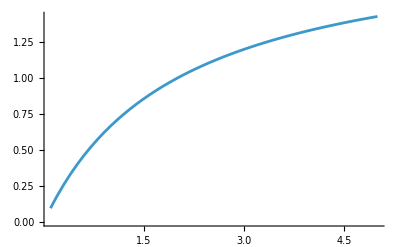

```mathematica
Plot[x((x^(α-1)(1+κ))/σ^α+(1-α)x^-1)(1+(κ x^α)/σ^α)^-1/.{κ->1,α->1,σ->2},{x,0.1,5}]
```

### Redefined Coupled Weibull with σ equal to the “Informational Scale”

```mathematica
GWDSF[σ_,κ_,α_,x_]:=(1+α κ x^α/σ^α)^(-1/(α κ));
```

```mathematica
GWDPDF[σ_,κ_,α_,x_]:=(α x^(α-1))/σ^α(1+α κ x^α/σ^α)^(-1/(α κ)-1);
```

```mathematica
-x D[GWDPDF[σ,κ,α,x],x]/GWDPDF[σ,κ,α,x]//FullSimplify
```

1+(α (x^α-σ^α))/(x^α α κ+σ^α)

```mathematica
1+(α (x^α-σ^α))/(x^α α κ+σ^α)/.x->σ//FullSimplify
```

1

### Score of Coupled Stretched Exponential Distribution

Computing - d Log[f(x)]/dx where f(x) is the Coupled Stretched Exponential Distribution.  The normalization, Z, can be ignored since the expression is equivalent to -d f’(x)/(f(x) dx) and constants cancel.

```mathematica
D[Log[(1+κ (x/σ)^α)^(- 1/α(1/κ+1))], x]//FullSimplify
```

-(x^(-1+α) (1+κ))/(x^α κ+σ^α)

```mathematica
(x^(-1+α) (1+κ))/(x^α κ+σ^α)/.x->σ//FullSimplify
```

1/σ

```mathematica
-x D[Log[(1+κ (x/σ)^α)^(- 1/α(1/κ+1))], x]//FullSimplify
```

((1+κ) (x/σ)^α)/(1+κ (x/σ)^α)

```mathematica
((1+κ) (x/σ)^α)/(1+κ (x/σ)^α)/.x->σ//FullSimplify
```

1

```mathematica
(1+κ) (1+κ (x/σ)^α)^(-1+(1+1/κ)/α) (x/σ)^α/.x->σ//FullSimplify
```

(1+κ)^((1+1/κ)/α)

### Multiplicative Noise Simulation

Define Stratonovich Process for Velocity with Multiplicative Noise and a Coupled Gaussian Limit Distribution

```mathematica
MultVelProc=StratonovichProcess[ⅆv[t]==-v[t]ⅆt+AⅆWAdd[t]+M v[t]ⅆWMult[t],v[t],{v,1},t,{WAdd\[Distributed]WienerProcess[],WMult\[Distributed]WienerProcess[]}]
```

StratonovichProcess[{{-v[t]},{{A,M v[t]}},v[t]},{{v},{1}},{t,0}]

```mathematica
MultVelProc["KolmogorovForwardEquation"]//TraditionalForm
```

p^(0,1)(v,t)==1/2 (∂^2 ((A^2+M^2 v^2) p(v,t)))/(∂v ∂v)-∂/(∂v)(1/2 (M^2 v-2 v) p(v,t))

```mathematica
Limit[PDF[MultVelProc[t]/.A->√2 σ,v]//FullSimplify,t->Infinity]
```

lim_(t→∞) PDF[StratonovichProcess[{{-v[t]},{{√2 σ,M v[t]}},v[t]^2},{{v},{1}},{t,0}][t],v]

```mathematica
AddSample[σ_,κ_]:=RandomFunction[AddVelProc/.{A->σ Sqrt[2],M->Sqrt[2*κ]},{0,10,.01},50];
```

```mathematica
MultSample[σ_,κ_]:=RandomFunction[MultVelProc/.{A->σ Sqrt[2],M->Sqrt[2*κ]},{0,10,.01},10];
```

σ = 2, κ = 0.1

```mathematica
Module[{σ=5,κ={0.1,1,10},yLimit={1,100}},
GraphicsRow[Table[
Show[
ListLinePlot[MultSample[σ,κ[[i]]],
PlotRange->{{0,10},{yLimit[[1]],yLimit[[2]]}},
PlotStyle->Thin,
ScalingFunctions->{"Linear","Log"},
LabelStyle->Bold,
Epilog->Inset["Coupling = "Text[κ[[i]]],{5,4}]
],
Plot[{Labeled[σ,"σ",{Bottom,Left}],
Labeled[σ/Sqrt[1+κ[[i]]],"β^(-FractionBox[1, 2])",{Top,Left}]},{x,0,10},
PlotRange->{{0,10},{yLimit[[1]],yLimit[[2]]}},
PlotStyle->Thick,
ScalingFunctions->{"Linear","Log"}
]
]
,{i,3}]]]
```

-Graphics-

#### Checking DeepSeek Solutions

```mathematica
Solve[1+τ/(α M)==(1+κ)/(α κ),κ]
```

{{κ→M/(-M+M α+τ)}}

```mathematica
M/(-M+M α+τ)A/M=A/(-M+M α+τ)

Solve[(τ+3/4 α M)/(α M)==(1+κ)/κ,κ]\\FullSimplify
```

Set::write: Tag Times in (A M)/(M (-M+M α+τ)) is Protected.

A/(-M+M α+τ)

```mathematica
Solve[(1+3/4 α M/τ)/(α M/τ)==(1+κ)/κ,κ]\\FullSimplify
```

Syntax::tsntxi: "Solve[(τ+3/4 αM)/αM==(1+κ)/κ,κ]\\FullSimplify" is incomplete; more input is needed.

```mathematica
Clear[A,M,α,τ]
```

### Check independent equals transformation

```mathematica
Solve[(1+(1+m)κ)/κ==(1+κM)/κM,κM]
```

{{κM→κ/(1+m κ)}}

```mathematica
Solve[1+1/M^2==1/2(1+1/κ),κ]
```

{}

```mathematica
2(1/2+1/M^2)==1/κ
```

```mathematica
κ==M^2/(1+M^2)
```

### Uncertainty at the Scale: Definition for Gen. Entropy

Since the generalized entropy must compute a solution that is equal to the generalized logarithm of the coupled stretched exponential distribution at the scale, it is illustrative to compute this value for a variety of generalized entropies. For simplicity the case of d=1, α = 1, and μ = 0 is computed. The entropy transformed to the domain of the distribution is exp_κ^(-(1+κ))[H]. This value must be set equal to f(x) and then one must solve for x, which requires taking ln_κ (f(x))^-1, reversing the coupled exponential.  So the equation setting H equal to the argument of the density. 
exp_κ^(-(1+κ))[H] = exp_κ^(-(1+κ))[x/σ+ln_κ σ^(1/(1+κ))+κ x/σ ln_κ σ^(1/(1+κ))]
H=x/σ(1+κ ln_κ σ^(1/(1+κ)))+ln_κ σ^(1/(1+κ))
x/σ=(σ(H-ln_κ σ^(1/(1+κ))))/(1+κ ln_κ σ^(1/(1+κ)))

```mathematica
entValue[H_,σ_,κ_]:=
σ(H-CoupledLogarithm[σ^(1/(1+κ)),κ,0])/(1+κ CoupledLogarithm[σ^(1/(1+κ)),κ,0])//FullSimplify;
```

```mathematica
entDensity[H_,κ_]:=
CoupledExponential[H,κ]^-1//FullSimplify;
```

```mathematica
HCoupled[σ_,κ_]:=1+CoupledLogarithm[σ,κ/(1+κ),0];
```

```mathematica
entValue[HCoupled[σ,κ],σ,κ]
```

σ

```mathematica
entDensity[HCoupled[σ,κ],κ]
```

(1+κ)^(-(1+κ)/κ)/σ

```mathematica
HBGS[σ_,κ_]:= 1+Log[σ]+κ;
```

```mathematica
entValue[HBGS[σ,κ],σ,κ]//FullSimplify
```

(σ^(1/(1+κ)) (1+κ+κ^2-σ^(κ/(1+κ))+κ Log[σ]))/κ

```mathematica
entDensity[HBGS[σ,κ],κ]
```

1/If[1+κ (1+κ+Log[σ])>0,If[κ≠0,(1+κ (1+κ+Log[σ]))^((1+1 κ)/κ),Exp[1+κ+Log[σ]]],If[(1+1 κ)/κ>0,0,∞]]

```mathematica
HRenyi[σ_,κ_]:= Log[σ]+(1+1/κ)Log[1+κ];
```

```mathematica
entValue[HRenyi[σ,κ],σ,κ]//FullSimplify
```

(σ^(1/(1+κ)) (1-σ^(κ/(1+κ))+(1+κ) Log[1+κ]+κ Log[σ]))/κ

```mathematica
entDensity[HRenyi[σ,κ],κ]
```

1/If[1+Log[1+κ]+κ Log[(1+κ) σ]>0,If[κ≠0,(1+κ ((1+1/κ) Log[1+κ]+Log[σ]))^((1+1 κ)/κ),Exp[(1+1/κ) Log[1+κ]+Log[σ]]],If[(1+1 κ)/κ>0,0,∞]]

```mathematica
HTsallis[σ_,κ_]:= 1 - 1/(1+κ)CoupledLogarithm[σ^-1,κ/(1+κ),0];
```

```mathematica
entValue[HTsallis[σ,κ],σ,κ]//FullSimplify
```

(σ^(1/(1+κ)) (2+κ-2 Cosh[(κ Log[σ])/(1+κ)]))/κ

```mathematica
entDensity[HTsallis[σ,κ],κ]
```

1/If[(2+κ) σ^(κ/(1+κ))>1,If[κ≠0,(1+κ (1-1/(1+κ)If[1/σ≥0,If[κ/(1+κ)≠0,((1/σ)^(κ/((1+κ) (1+(0 κ)/(1+κ))))-1)/(κ/(1+κ)),Log[1/σ]],Undefined]))^((1+1 κ)/κ),Exp[1-1/(1+κ)If[1/σ≥0,If[κ/(1+κ)≠0,((1/σ)^(κ/((1+κ) (1+(0 κ)/(1+κ))))-1)/(κ/(1+κ)),Log[1/σ]],Undefined]]],If[(1+1 κ)/κ>0,0,∞]]

```mathematica
HNormTsallis[σ_,κ_]:= 1 + (1+κ)CoupledLogarithm[σ,κ/(1+κ),0]+κ;
```

```mathematica
entValue[HNormTsallis[σ,κ],σ,κ]
```

(σ^(-1+2/(1+κ)) ((1+κ)^2-κ σ^(κ/(1+κ))-σ^((2 κ)/(1+κ))))/κ

```mathematica
entDensity[HNormTsallis[σ,κ],κ]
```

1/If[(1+κ)^2>κ σ^(κ/(1+κ)),If[κ≠0,(1+κ (1+κ+(1+κ) If[1/σ≥0,If[κ/(1+κ)≠0,((1/σ)^(κ/((1+κ) (1+(0 κ)/(1+κ))))-1)/(κ/(1+κ)),Log[1/σ]],Undefined]))^((1+1 κ)/κ),Exp[1+κ+(1+κ) If[1/σ≥0,If[κ/(1+κ)≠0,((1/σ)^(κ/((1+κ) (1+(0 κ)/(1+κ))))-1)/(κ/(1+κ)),Log[1/σ]],Undefined]]],If[(1+1 κ)/κ>0,0,∞]]

```mathematica
Module[{EntData,σPlotBottom=0.5,σPlotTop=2,
κValues={1/2,1,2}},
EntData=Table[
Table[{entValue[entName[σPlot,κPlot],σPlot,κPlot],
entDensity[entName[σPlot,κPlot],κPlot]},
{σPlot,{σPlotBottom,σPlotTop}},{κPlot,κValues}],
{entName,{HCoupled,HBGS,HRenyi,HTsallis,HNormTsallis}}
];
ResourceFunction["PlotGrid"][
{{Plot[
Table[PDF[CoupledExponentialDistribution[σPlotTop,κPlot],x],
{κPlot,κValues}]
,{x,0,7.5},
PlotRange->{{0,5},{0,0.55}},
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Bold,Medium],
Epilog->{
{Dashed,Gray,Line[{{σPlotTop,0},{σPlotTop,0.6}}]},
PointSize[Large],
{Black,Point[EntData[[1,2]]]},
{Blue,Point[EntData[[2,2]]]},
{Brown,Point[EntData[[3,2]]]},
{Magenta,Point[EntData[[4,2]]]},
{Orange,Point[EntData[[5,2]]]},
Inset[Style["Required Solution",
Medium],{2.8,0.32}],
Inset[Style["= Coupled Entropy",
Medium],{3.0,0.28}],
Inset[Style["BGS",Blue,Medium],{3.0,0.12}],
Inset[Style["Renyi",Brown,Medium],{2.5,0.16}],
Inset[Style["Tsallis",Magenta,Medium],{1,0.12}],
Inset[Style["Norm Tsallis",Orange,Medium],{4.0,0.1}] ,
Inset[Style["σ",Black,Medium],{1.9,0.03}],
Inset[Style["Coupled Exponential",Black, Medium, Bold],
Scaled[{0.77,0.92}]],
Inset[Style["κ = 0.5, 1, 2, σ = 2",Black, Medium, Bold],
Scaled[{0.77,0.84}]],
Inset[Style["Higher κ → Lower f(x(H))",Black, Medium, Bold],
Scaled[{0.77,0.76}]],
Inset[Style["a)",Black, Medium],
Scaled[{0.03,0.95}]]
}
]},
{Plot[
Table[PDF[CoupledExponentialDistribution[σPlotBottom,κPlot],x],
{κPlot,κValues}]
,{x,0,5},
PlotRange->{{0,2.5},{0,1.05}} ,
Frame->{{True,True},{True,True}},
FrameStyle->Directive[Bold,Medium],
Epilog->{
{Dashed,Gray,Line[{{σPlotBottom,0},{σPlotBottom,1.0}}]},
PointSize[Large],
{Black,Point[EntData[[1,1]]]},
{Blue,Point[EntData[[2,1]]]},
{Brown,Point[EntData[[3,1]]]},
{Magenta,Point[EntData[[4,1]]]},
{Orange,Point[EntData[[5,1]]]},
Inset[Style["Required Solution",
Medium],{0.9,0.77}],
Inset[Style["= Coupled Entropy",
Medium],{0.92,0.69}],
Inset[Style["BGS",Blue,Medium],{1.3,0.22}],
Inset[Style["Renyi",Brown,Medium],{0.8,0.5}],
Inset[Style["Tsallis",Magenta,Medium],{0.68,0.2}],
Inset[Style["Norm Tsallis",Orange,Medium],{1.15,0.35}],
Inset[Style["σ",Black,Medium],{0.55,0.05}],
Inset[Style["Coupled Exponential",Black, Medium, Bold],
Scaled[{0.77,0.92}]],
Inset[Style["κ = 0.5, 1, 2, σ = 0.5",Black, Medium, Bold],
Scaled[{0.77,0.84}]],
Inset[Style["Higher κ → Lower f(x(H))",Black, Medium, Bold],
Scaled[{0.77,0.76}]],
Inset[Style["b)",Black, Medium],
Scaled[{0.03,0.95}]]
}
]}},
Spacings->20,
FrameLabel->{"x","Density, f(x)"},
PlotLabel->"Entropies Mapped to Density"
]]
```

OptionValue::nodef: Unknown option DefaultBaseStyle for Graphics.

General::stop: Further output of OptionValue::nodef will be suppressed during this calculation.

-Graphics-

Saved Plots

### Moments of Coupled Weibull distribution

Keeping 1+α κ term

```mathematica
∫x^α α/σ(x/σ)^(α-1)Exp[-(1+α κ)(x/σ)^α]ⅆx//FullSimplify
```

-(σ^α Gamma[2,(1+α κ) (x/σ)^α])/(1+α κ)^2

```mathematica
-(σ^α Gamma[2,(1+α κ) (x/σ)^α])/(1+α κ)^2/.x->0//FullSimplify
```

-σ^α/(1+α κ)^2

```mathematica
-σ^α/(1+α κ)^2/.{σ^α->σ^α/(1+α κ),κ->κ/(1+α κ)}//FullSimplify
```

-((1+α κ) σ^α)/(1+2 α κ)^2

Removing 1+α κ term

```mathematica
∫x^α α/σ(x/σ)^(α-1)Exp[-(x/σ)^α]ⅆx//FullSimplify
```

-σ^α Gamma[2,(x/σ)^α]

```mathematica
-σ^α Gamma[2,(x/σ)^α]/.x->0//FullSimplify
```

-σ^α

```mathematica
-σ^α/(1+α κ) Gamma[2,(1+α κ)(x/σ)^α]/.x->0//FullSimplify
```

-σ^α/(1+α κ)

```mathematica
∫x^(-1/κ-1)ⅆx
```

-x^(-1/κ) κ

```mathematica
Limit[-x^(-1/κ) κ,x->∞]
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

0

### Fluctuation Model

Syntax::sntxi: Incomplete expression; more input is needed.

```mathematica
∫_0^1 Exp[-t/σ]PDF[GammaDistribution[1/κ,κ/σ],1/t]ⅆt
```

∫_0^1 (ⅇ^(-t/σ))^x (Piecewise[{{(ⅇ^(-σ/(t κ)) (1/t)^(-1+1/κ) (κ/σ)^(-1/κ))/Gamma[1/κ], 1/t>0}, {0, True}}])ⅆt

```mathematica
∫_0^∞ c Exp[-c t]PDF[GammaDistribution[1/κ,κ β],c]ⅆc
```

Piecewise[{{(β^(1-1/κ) (1/β+t κ)^(-1/κ))/(1+t β κ), Re[t+1/(β κ)]>0}, {Integrate[c ⅇ^(-c t) (Piecewise[{{(c^(-1+1/κ) ⅇ^(-c/(β κ)) (β κ)^(-1/κ))/Gamma[1/κ], c>0}, {0, True}}]),{c,0,∞},Assumptions→d∈ℤ&&x∈ℝ&&α∈ℝ&&κ∈ℝ&&μ∈ℝ&&σ∈ℝ&&κ>0&&σ>0&&α>0&&d>0&&Re[t+1/(β κ)]≤0], True}}]

```mathematica
Piecewise[{{(β^(1-1/κ) (1/β+t κ)^(-1/κ))/(1+t β κ), Re[t+1/(β κ)]>0}, {Integrate[c ⅇ^(-c t) (Piecewise[{{(c^(-1+1/κ) ⅇ^(-c/(β κ)) (β κ)^(-1/κ))/Gamma[1/κ], c>0}, {0, True}}]),{c,0,∞},Assumptions->d∈Integers&&x∈Reals&&α∈Reals&&κ∈Reals&&μ∈Reals&&σ∈Reals&&κ>0&&σ>0&&α>0&&d>0&&Re[t+1/(β κ)]≤0], True}}]//FullSimplify
```

Piecewise[{{(β^(1-1/κ) (1/β+t κ)^(-1/κ))/(1+t β κ), Re[t+1/(β κ)]>0}, {Integrate[c ⅇ^(-c t) (Piecewise[{{(c^(-1+1/κ) ⅇ^(-c/(β κ)) (β κ)^(-1/κ))/Gamma[1/κ], c>0}, {0, True}}]),{c,0,∞},Assumptions→d∈ℤ&&x∈ℝ&&α∈ℝ&&κ∈ℝ&&μ∈ℝ&&σ∈ℝ&&κ>0&&σ>0&&α>0&&d>0&&Re[t+1/(β κ)]≤0], True}}]

```mathematica
β^1 (1+t β κ)^(-1/κ-1)
```

```mathematica
∫_0^∞ c Exp[-c t^2]PDF[GammaDistribution[1/κ,κ β],c]ⅆc
```

Piecewise[{{(β^(1-1/κ) (1/β+t^2 κ)^(-1/κ))/(1+t^2 β κ), Re[t^2+1/(β κ)]>0}, {Integrate[c ⅇ^(-c t^2) (Piecewise[{{(c^(-1+1/κ) ⅇ^(-c/(β κ)) (β κ)^(-1/κ))/Gamma[1/κ], c>0}, {0, True}}]),{c,0,∞},Assumptions→d∈ℤ&&x∈ℝ&&α∈ℝ&&κ∈ℝ&&μ∈ℝ&&σ∈ℝ&&κ>0&&σ>0&&α>0&&d>0&&Re[t^2+1/(β κ)]≤0], True}}]

```mathematica
∫_0^∞ c Exp[-c^2 t^2]PDF[GammaDistribution[1/κ,κ β^2],c]ⅆc
```

Piecewise[{{-1/(4 Gamma[1/κ])(t^2)^(-3/2-1/(2 κ)) (β^2)^(-1-1/κ) κ^(-2-1/κ) (√(t^2) Gamma[1/(2 κ)] Hypergeometric1F1[1+1/(2 κ),3/2,1/(4 t^2 β^4 κ^2)]-2 t^2 β^2 κ^2 Gamma[(1+κ)/(2 κ)] Hypergeometric1F1[(1+κ)/(2 κ),1/2,1/(4 t^2 β^4 κ^2)]), (Re[t^2]≥0&&Re[β^2]>0)||Re[t^2]>0}, {Integrate[c ⅇ^(-c^2 t^2) (Piecewise[{{(c^(-1+1/κ) ⅇ^(-c/(β^2 κ)) (β^2 κ)^(-1/κ))/Gamma[1/κ], c>0}, {0, True}}]),{c,0,∞},Assumptions→(d∈ℤ&&x∈ℝ&&α∈ℝ&&κ∈ℝ&&μ∈ℝ&&σ∈ℝ&&Re[t^2]≤0&&d>0&&α>0&&κ>0&&σ>0&&Re[β^2]≤0)||(d∈ℤ&&x∈ℝ&&α∈ℝ&&κ∈ℝ&&μ∈ℝ&&σ∈ℝ&&Re[t^2]<0&&d>0&&α>0&&κ>0&&σ>0)], True}}]

```mathematica
∫_∞^0 1/c Exp[-1/c t^2]PDF[GammaDistribution[1/κ,κ/σ^2],1/c]ⅆ(1/c)
```

Integrate::ilim: Invalid integration variable or limit(s) in {1/c,∞,0}.

∫_∞^0 (ⅇ^(-t^2/c) (Piecewise[{{((1/c)^(-1+1/κ) ⅇ^(-σ^2/(c κ)) (κ/σ^2)^(-1/κ))/Gamma[1/κ], 1/c>0}, {0, True}}]))/c ⅆ 1/c

```mathematica
∫_0^∞ c Exp[-c t^α]PDF[GammaDistribution[1/κ,κ β],c]ⅆc
```

Piecewise[{{(β^(1-1/κ) (1/β+t^α κ)^(-1/κ))/(1+t^α β κ), Re[t^α+1/(β κ)]>0}, {Integrate[c ⅇ^(-c t^α) (Piecewise[{{(c^(-1+1/κ) ⅇ^(-c/(β κ)) (β κ)^(-1/κ))/Gamma[1/κ], c>0}, {0, True}}]),{c,0,∞},Assumptions→d∈ℤ&&x∈ℝ&&α∈ℝ&&κ∈ℝ&&μ∈ℝ&&σ∈ℝ&&κ>0&&σ>0&&α>0&&d>0&&Re[t^α+1/(β κ)]≤0], True}}]

```mathematica
∫_0^∞ Exp[-c t^α]PDF[GammaDistribution[1/κ+1,κ/(1+κ) β^α],c]ⅆc
```

$Aborted

### Complexity Measurement

Determine the Taylor Series expansion of the result

```mathematica
EntRatioExp = (1+Log[ σ (1-κ)])/(1+Log[ σ ])
```

(1+Log[(1-κ) σ])/(1+Log[σ])

```mathematica
Series[EntRatioExp(1-EntRatioExp),{κ,0,3},
Assumptions->(0<κ<1)]
```

κ/(1+Log[σ])+((-1+Log[σ]) κ^2)/(2 (1+Log[σ])^2)+((-2+Log[σ]) κ^3)/(3 (1+Log[σ])^2)+O[κ]^4

```mathematica
Series[-(1+Log[1-κ]/Log[σ])(Log[1-κ]/Log[σ]),{κ,0,3},
Assumptions->(0<κ<1/2)]
```

κ/Log[σ]+((-2+Log[σ]) κ^2)/(2 Log[σ]^2)+((-3+Log[σ]) κ^3)/(3 Log[σ]^2)+O[κ]^4

First order approximation of the entropy of the coupled Gaussian with σ=1

```mathematica
Series[(1+κ)/(2κ)(PolyGamma[(1+κ)/(2κ)]-PolyGamma[1/(2κ)])+
Log[1/(√κ)Beta[1/(2κ),1/2]],{κ,0,3}]//FullSimplify
```

1/2 (1+Log[2]+Log[π])+κ+κ^2/4-κ^3/6+O[κ]^(7/2)

Taylor Series of Complexity of Coupled Gaussian

```mathematica
EntRatioGauss = (1/2+1/2 Log[2π σ √(1-2κ)])/(1/2+1/2 Log[2π σ])
```

(1/2+1/2 Log[2 π √(1-2 κ) σ])/(1/2+1/2 Log[2 π σ])

```mathematica
Series[EntRatio(1-EntRatioGauss),{κ,0,3}]
```

κ/(1+Log[2 π σ])+(Log[2 π σ] κ^2)/(1+Log[2 π σ])^2+(2 (-1+2 Log[2 π σ]) κ^3)/(3 (1+Log[2 π σ])^2)+O[κ]^4

## Relation to c,d-entropy

### Asymptotic Classification

J. M. Amigó, S. G. Balogh, and S. Hernández, “A Brief Review of Generalized Entropies,” Entropy, vol. 20, no. 11, p. 813, Nov. 2018, doi: 10.3390/e20110813.

For Coupled Entropy, consider that for p_i=1/W, the independent equals distribution also equals p_i. Then g(x) = x ln_(α κ)x^(-1/(1+κ))=x/(α κ)x^(-α κ/(1+κ))+O(x) = 1/(α κ)x^(1-α κ/(1+κ))+O(x) = 1/(α κ)x^(2-q)+O(x)
and G(u) = u^(1/γ).

```mathematica
g[r_,κ_,α_,d_]:=1/(α κ)r^(1-(α κ)/(1+d κ));
G[u_,γ_]:=u^(1/γ);
```

```mathematica
Limit[G[λ W g[1/(λ W),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ],W->∞]
```

ConditionalExpression[((1/λ)^(-(α κ)/(1+d κ)))^(1/γ), ]

```mathematica
(λ^((α κ/γ)/(1+d κ)))=λ^(1-c)
```

c = 1 - (α κ/γ)/(1+d κ)

```mathematica
Limit[G[ W^(1+a) g[1/W^(1+a),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ] W^(-a(α κ/γ)/(1+d κ)),W->∞]
```

ConditionalExpression[1, 1/γ∈ℝ&&a>-1&&d κ>-1&&α κ>0]

Thus for (1+a)^d=1, d = 0.

```mathematica
G[ W^(1+a) g[1/W^(1+a),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ] W^(-a(α κ/γ)/(1+d κ))//FullSimplify
```

((1/W)^(-(α κ)/(1+d κ)))^(-1/γ) W^(-(a α κ)/(γ+d γ κ)) ((W^(-1-a))^(-(α κ)/(1+d κ)))^(1/γ)

(W^(-(α κ)/((1+d κ)γ)))W^(-(a α κ)/(γ+d γ κ))W^(((1+a)α κ)/((1+d κ)γ))

```mathematica
-(α κ)/((1+d κ)γ)-(a α κ)/(γ+d γ κ)+((1+a)α κ)/((1+d κ)γ)//FullSimplify
```

0

```mathematica
Limit[G[ W^(1+a) g[1/W^(1+a),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ] W^(-a(1-c)),W->∞]
```

ConditionalExpression[∞, ]

```mathematica
Limit[G[ W^(1+a) g[1/W^(1+a),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ] W^(-a(1-1)),W->∞]
```

ConditionalExpression[∞, a>0]

```mathematica
Limit[G[ W^(1+a) g[1/W^(1+a),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ] W^(-a(1-0)),W->∞]
```

ConditionalExpression[∞, a>-1&&a≠0&&a γ (1+d κ)<a α κ]

What if the full form of the generalized logarithm is used?

For Coupled Entropy, consider that for p_i=1/W, the independent equals distribution also equals p_i. Then g(x) = x ln_(α κ)x^(-1/(1+κ))=x/(α κ)(x^(-α κ/(1+κ))-1)

```mathematica
g[r_,κ_,α_,d_]:=r/(α κ)(r^(-(α κ)/(1+d κ))-1);
G[u_,γ_]:=u^(1/γ);
```

```mathematica
Limit[G[λ W g[1/(λ W),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ]//FullSimplify,W->∞]
```

((1/λ)^(-(α κ)/(1+d κ)))^(1/γ)

```mathematica
Limit[G[ W^(1+a) g[1/W^(1+a),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ] W^(-a(α κ/γ)/(1+d κ))//FullSimplify,W->∞]
```

ConditionalExpression[1, a>1]

```mathematica
G[ W^(1+a) g[1/W^(1+a),κ,α,d],γ]/G[W g[1/W,κ,α,d],γ] W^(-a(α κ/γ)/(1+d κ))//FullSimplify
```

(-1+(1/W)^(-(α κ)/(1+d κ)))^(-1/γ) W^(-(a α κ)/(γ+d γ κ)) (-1+(W^(-1-a))^(-(α κ)/(1+d κ)))^(1/γ)

With W -> ∞ only the terms with W are significant and all the terms contain (α κ)/(γ(1+d κ)). Thus exponent multiplies this by (1 - a -1 -a) = 0, which is why the expression converges to 1. But if κ -> 0 first, then the -1 term is of significance in the terms converging to log W^z. Set r = (α κ)/(1+d κ), and factor out the 1+a from the coupled logarithm, then the ratio is ((1+a) ln_(-r(1+a))W)/(ln_-r W). The question is under what circumstance does this ratio converge to 1 + a?  Certainly when r ->0  first.  What about when r -> 1, which is its other limit? Then Lim_(W->∞)((1+a)(W^(-(1+a))-1))/((1+a) (W^-1-1))=1 .

Try using the form e^(W^(1+a)) and see what the scaling is

```mathematica
Limit[G[ Exp[W^(1+a)] g[1/Exp[W^(1+a)],κ,α,d],γ]/G[Exp[W] g[1/Exp[W],κ,α,d],γ] Exp[W^(-a(α κ/γ)/(1+d κ))],W->∞]
```

lim_(W→∞) (ⅇ^(W^(-(a α κ)/(γ (1+d κ)))) G[ⅇ^(W^(1+a)) g[ⅇ^(-W^(1+a)),κ,α,d],γ])/G[ⅇ^W g[ⅇ^-W,κ,α,d],γ]

```mathematica
Limit[G[ Exp[W^a] g[1/Exp[W^a],κ,α,d],γ]/G[Exp[W] g[1/Exp[W],κ,α,d],γ],W->∞]
```

lim_(W→∞) G[ⅇ^(W^a) g[ⅇ^(-W^a),κ,α,d],γ]/G[ⅇ^W g[ⅇ^-W,κ,α,d],γ]

### Taylor series of coupled exponential function

```mathematica
Series[CoupledExponential[x,κ,1],{x,x0,4}]
```

Piecewise[{{∞, (x∈ℝ&&-1≤κ<0&&x0 κ<-1)||(x0∈ℝ&&κ≠0&&x0 κ==-1&&x κ≤-1&&-1≤κ<0)}, {((x-x0) κ)^(1/κ) (κ (x-x0)+O[x-x0]^5), x0∈ℝ&&κ≠0&&x0 κ==-1&&((κ>0&&x κ>-1)||(κ<0&&x κ>-1))}, {ⅇ^x0+ⅇ^x0 (x-x0)+1/2 ⅇ^x0 (x-x0)^2+1/6 ⅇ^x0 (x-x0)^3+1/24 ⅇ^x0 (x-x0)^4+O[x-x0]^5, (x|x0)∈ℝ&&κ==0}, {(1+x0 κ)^(1+1/κ)+(1+κ) (1+x0 κ)^(1/κ) (x-x0)+1/2 (1+κ) (1+x0 κ)^(-1+1/κ) (x-x0)^2-1/6 ((-1+κ) (1+κ) (1+x0 κ)^(-2+1/κ)) (x-x0)^3+1/24 (1+κ) (1+x0 κ)^(-3+1/κ) (1-3 κ+2 κ^2) (x-x0)^4+O[x-x0]^5, x∈ℝ&&((κ>0&&x0 κ>-1)||(κ<0&&x0 κ>-1))}, {0, True}}]

### Taylor series of cdFunction

Starting with the 0th branch which corresponds to d>0

```mathematica
cdFuntion[x_,c_,d_,r_]:=
Exp[-d/(1-c)(ProductLog[0,B[c,r](1-x/r)^(1/d)]
-ProductLog[0,B[c,r]])]/;d>0;
```

```mathematica
B[c_,r_]:=((1-c)r)/(1-(1-c)r)Exp[((1-c)r)/(1-(1-c)r)];
```

```mathematica
Series[ProductLog[0,z],{z,z0,4}]
```

ProductLog[z0]+(ProductLog[z0] (z-z0))/(z0 (1+ProductLog[z0]))-((ProductLog[z0]^2 (2+ProductLog[z0])) (z-z0)^2)/(2 (z0^2 (1+ProductLog[z0])^3))+(ProductLog[z0]^3 (9+8 ProductLog[z0]+2 ProductLog[z0]^2) (z-z0)^3)/(6 z0^3 (1+ProductLog[z0])^5)+(ProductLog[z0]^4 (-64-79 ProductLog[z0]-36 ProductLog[z0]^2-6 ProductLog[z0]^3) (z-z0)^4)/(24 z0^4 (1+ProductLog[z0])^7)+O[z-z0]^5

```mathematica
Series[cdFuntion[x,c,d,r],{x,x0,4}]
```

ⅇ^((d (-ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r)/(1+(-1+c) r)]+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]))/(-1+c))-(ⅇ^((d (-ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r)/(1+(-1+c) r)]+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]))/(-1+c)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)] (x-x0))/((-1+c) (r-x0) (1+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]))-((ⅇ^((d (-ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r)/(1+(-1+c) r)]+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]))/(-1+c)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)] (1-c-d+c d-3 d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]+2 c d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]-2 d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2+c d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2)) (x-x0)^2)/(2 ((-1+c)^2 d (r-x0)^2 (1+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)])^3))-((ⅇ^((d (-ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r)/(1+(-1+c) r)]+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]))/(-1+c)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)] (1-2 c+c^2-3 d+6 c d-3 c^2 d+2 d^2-4 c d^2+2 c^2 d^2-2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]+4 c ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]-2 c^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]-9 d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]+15 c d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]-6 c^2 d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]+11 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]-19 c d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]+8 c^2 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]-6 d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2+9 c d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2-3 c^2 d ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2+22 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2-33 c d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2+12 c^2 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2+19 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^3-25 c d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^3+8 c^2 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^3+6 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^4-7 c d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^4+2 c^2 d^2 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^4)) (x-x0)^3)/(6 ((-1+c)^3 d^2 (r-x0)^3 (1+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)])^5))+(ⅇ^((d (-ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r)/(1+(-1+c) r)]+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]))/(-1+c)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)] (-(-1+c)^3 (-1+6 d-11 d^2+6 d^3)-(-1+c)^2 (-1+d) (8+15 d-47 d^2+4 c (-2-2 d+9 d^2)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]-(-1+c) (-1+d) (6+25 d+151 d^2+6 c^2 (1+4 d+15 d^2)-c (12+49 d+235 d^2)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^2+d (c (52+252 d-604 d^2)+c^3 (12+44 d-120 d^2)+5 (-4-22 d+51 d^2)+2 c^2 (-22-93 d+235 d^2)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^3+d^2 (-35+c (75-526 d)+c^3 (11-90 d)+239 d+c^2 (-51+380 d)) ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^4+(118-242 c+163 c^2-36 c^3) d^3 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^5+(24-46 c+29 c^2-6 c^3) d^3 ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)]^6) (x-x0)^4)/(24 (-1+c)^4 d^3 (r-x0)^4 (1+ProductLog[-((-1+c) ⅇ^((r-c r)/(1+(-1+c) r)) r (1-x0/r)^(1/d))/(1+(-1+c) r)])^7)+O[x-x0]^5